```mathematica
Clear["Global`*"];
```

```mathematica
BasisFunction[n_]:=Function[{x},√((2n+1)/2)LegendreP[n,x]];
BasisMax=10;
Plot[Evaluate[Table[BasisFunction[n][x],{n,0,BasisMax}]],{x,-1,1},ImageSize->Medium];
```

```mathematica
LegendreToCartesianBasis[y_]:=y.Table[BasisFunction[n][x],{n,0,BasisMax}];
```

```mathematica
qFunction[x_]=PDF[NormalDistribution[0.1,0.2],x];
q=Table[NIntegrate[qFunction[x]BasisFunction[n][x],{x,-1,1}],{n,0,BasisMax}];
Plot[{qFunction[x],LegendreToCartesianBasis[q]},{x,-1,1},PlotRange->All];
```

```mathematica
(LegendreDerivativeMatrixPrecalc=Transpose[Sum[DiagonalMatrix[Table[2i+1,{i,0,BasisMax-1}][[;;BasisMax-(i-1)]],i],{i,1,BasisMax,2}]])//MatrixForm;
(LegendreDerivativeMatrix=Transpose[MapIndexed[#1 √((2#2[[1]]-1)/(2#2[[2]]-1))&,LegendreDerivativeMatrixPrecalc,{2}]])//MatrixForm;
(LegendreSecondDerivativeMatrix=MatrixPower[LegendreDerivativeMatrix,2])//MatrixForm;
{Plot[Evaluate[{D[qFunction[x], x],LegendreToCartesianBasis[LegendreDerivativeMatrix.q]}],{x,-1,1}],
Plot[Evaluate[{D[qFunction[x], x,x],LegendreToCartesianBasis[LegendreSecondDerivativeMatrix.q]}],{x,-1,1}]};
```

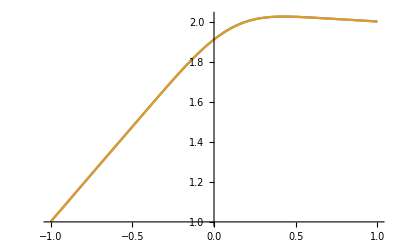

```mathematica
(* y[-1] = a, y[1] = b *)
a=1;
b=2;
AnaliticalSolution=y/.NDSolve[{D[y[x], x,x]==-qFunction[x],y[-1]==a,y[1]==b},y,{x,-1,1}][[1]];
BasisSolution=-Inverse[LegendreSecondDerivativeMatrix[[;;-3,3;;]]].(q[[;;-3]]);
BasisSolution=Flatten[{c0,c1}~Join~BasisSolution];
BasisSolution=BasisSolution/.Solve[
{(LegendreToCartesianBasis[BasisSolution]/.x->-1)==a,
(LegendreToCartesianBasis[BasisSolution]/.x->+1)==b},
{c0,c1}];
Plot[Evaluate[{AnaliticalSolution[x],LegendreToCartesianBasis[BasisSolution]}],{x,-1,1}]
```

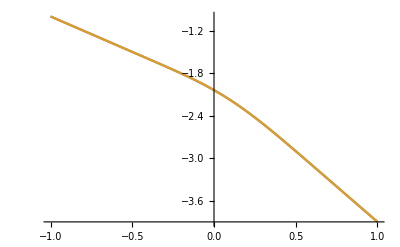

```mathematica
(* y[-1] = a, y'[-1] = b *)
a=-1;
b=-1;
AnaliticalSolution=y/.NDSolve[{D[y[x], x,x]==-qFunction[x],y[-1]==a,y'[-1]==b},y,{x,-1,1}][[1]];
BasisSolution=-Inverse[LegendreSecondDerivativeMatrix[[;;-3,3;;]]].(q[[;;-3]]);
BasisSolution=Flatten[{c0,c1}~Join~BasisSolution];
BasisSolution=BasisSolution/.Solve[
{(LegendreToCartesianBasis[BasisSolution]/.x->-1)==a,
(LegendreToCartesianBasis[LegendreDerivativeMatrix.BasisSolution]/.x->-1)==b},
{c0,c1}];
Plot[Evaluate[{AnaliticalSolution[x],LegendreToCartesianBasis[BasisSolution]}],{x,-1,1}]
```